E3max-E3min       = 0.0544942

normE1E3          = 1.34468×10^-7

IntE1E3           = 0.732238

Phace Space(E1*E3)=9.84625×10^-8

normM12           = 7.17623×10^-11

IntM12            =4.92312×10^-8

Phace Space(M12)  =3.53295×10^-18

Ratio(M12/ME1E3)  =3.58811×10^-11

Ratio(ME1E3/M12)  =2.78698×10^10

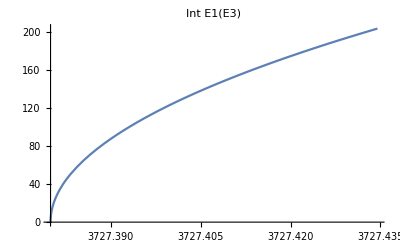

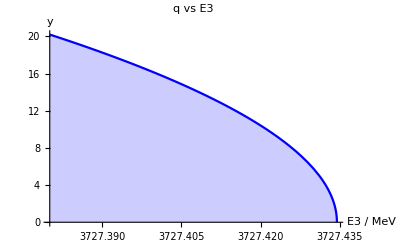

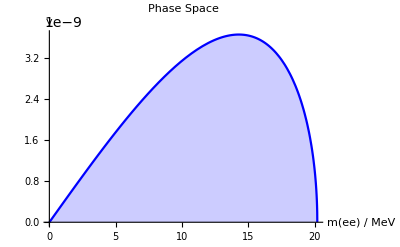

```mathematica
mbe8=8.005305*931.5;
mbe8s=mbe8+18.15;
mhe4=3727.38;
mhe4s=mhe4+20.21;
m=mhe4s;
m3=mhe4;
me=0.51099907;
me=0.0;
m1=me;
q2min=(2me)^2;
q2max=(m-m3)^2;
qmin=2 me;
qmax=m-m3;


e3[q_]:=(m^2+m3^2-q^2)/(2m);
p3[q_]:=Sqrt[(m^2-(m3+q)^2)(m^2-(m3-q)^2)]/(2*m);
eq[q_]:=(m^2-m3^2+q^2)/(2m);
pq[q_]:=p3[q];

p1s[q_]:=Sqrt[q^2/4-me^2];
p2s[q_]:=Sqrt[q^2/4-me^2];
e1s[q_]:=q/2.;
e2s[q_]:=q/2.;
gamma[q_]=eq[q]/q;
vel[q_]:=(Sqrt[eq[q]^2-q^2]/eq[q]);

e1min[q_]:=eq[q]/2.-pq[q]/2.;
e1max[q_]:=eq[q]/2.+pq[q]/2.;

(*
e1[q_,cos_]  :=gamma[q]*(e1s[q]+vel[q]*p1s[q]*cos);
e2[q_,cos_]  :=gamma[q]*(e1s[q]-vel[q]*p1s[q]*cos);
*)
e1[q_,cos_]  :=eq[q]/2+pq[q]/2*cos;
e2[q_,cos_]  :=eq[q]/2-pq[q]/2*cos;
p1z[q_,cos_]:=pq[q]/2+eq[q]/2cos;
p2z[q_,cos_]:=pq[q]/2-eq[q]/2cos;
p1x[q_,cos_]:=p1s[q]Sqrt[1.-cos^2];
p2x[q_,cos_]:=-p1s[q]Sqrt[1.-cos^2];

p1[q_,cos_]  :=e1[q,cos];
p2[q_,cos_]  :=e2[q,cos];

e3min=e3[qmax];
e3max=e3[qmin];

p3q[q_]:=(m^2-m3^2-q^2)/2.;
p1q[q_]:=q^2/2.;
p1p2[q_]:=(q^2-2me^2)/2.;

p3p1[q_,cos_]:=e3[q]*e1[q,cos]+p3[q]*p1z[q,cos];
p3p2[q_,cos_]:=e3[q]*e2[q,cos]+p3[q]*p2z[q,cos];

mtest[q_,cos_]:=2*p3p1[q,cos]*p3p2[q,cos]-m3^2*q^2/2. ;
mtesti[q_]:=NIntegrate[mtest[q,c],{c,-1,1}];

mel0[q_,cc_]:=0.125 (1-cc^2)(m^4+m3^4-2m3^2q^2+q^4-2m^2(m3^2+q^2));
mel0i[q_]:=Integrate[mel0[q,cc],{cc,-1,1}];

n2=(m^2-m3^2)^2*(1/6);
(*
me2[q_]:=(4 Pi)^2*[2*((m*gamma[q])^2*(e1s[q]^2-(vel[q]*p1s[q]*2/3))^2)-m3^2*(q^2-2 me^2)/2-me^2*m3^2);

meold2[q_]:=(4 Pi)(2*((m*gamma[q])^2*(e1s[q]^2-(vel[q]*p1s[q])^2*(2/3)))-m3^2*(q^2-2 me^2)/2-me^2*m3^2);
*)
me2[q_]:=2*(2*( (m^2-m3^2-q^2)/4)^2-(m3*q)^2/2)-2*(2/3)*(m*pq[q]/(2))^2;

phs[q_]:= p3[q]*p1s[q];

me1[q_,cos_]:=(2*( (m^2-m3^2-q^2)/4)^2-(m3*q)^2/2)-2*cos^2*(m*pq[q]/(2))^2;
mme1[q_]:=Integrate[me1[q,cc],{cc,-1,1}];


phs[q_]:= p3[q]*p1s[q]*(4 π)(2π)/(2π)^5/(16 m^2);

normphsp=1./(2*Pi)^5/(16*m^2)*4*Pi*2*Pi;
normme2=(4*Pi)^2;
normone=8*Pi/(m^5*5.97*10^(-13));
norm=normphsp*normme2*normone;

dgdq[q_]    :=me2[q]*phs[q];
dgdq2[q2_]:=dgdq[Sqrt[q2]]/(2*Sqrt[q2]);
                                    
            (*  *****    Phace Space E1E3 *****   *)
inte1[x3_]:=Module[{q}
,q=Sqrt[(m-x3)*2*m-(m^2-m3^2)];NIntegrate[x1,{x1,e1min[q],e1max[q]}]];
 
normE1E3=(1/(2*Pi)^3)*(1/(8*m));
IntE1E3=NIntegrate[1,{x3,e3min,e3max},{x1,e1min[Sqrt[2m(m-x3)-(m^2-m3^2)]],e1max[Sqrt[2m(m-x3)-(m^2-m3^2)]]}];
             (*  *****    Phace Space M12 *****   *)
normM12=(1/(2*Pi)^5)*(1/(16*m^2))*4Pi*4Pi;
IntM12=NIntegrate[phs[q],{q,qmin,qmax}];


Print["E3max-E3min       = ",e3max-e3min]
Print["normE1E3          = ",normE1E3]
Print["IntE1E3           = ",IntE1E3]
Print["Phace Space(E1*E3)=",IntE1E3*normE1E3]
Print["normM12           = ",normM12]
Print["IntM12            =",IntM12]
Print["Phace Space(M12)  =",IntM12*normM12]
Print["Ratio(M12/ME1E3)  =",IntM12*normM12/(IntE1E3*normE1E3)]
Print["Ratio(ME1E3/M12)  =",IntE1E3*normE1E3/(IntM12*normM12)]


Plot[inte1[x3],{x3,e3min,e3max},PlotLabel->"Int E1(E3)"]
Plot[Sqrt[2m(m-x3)-(m^2-m3^2)],{x3,e3min,e3max},
PlotLabel->"q vs E3",
FrameLabel->{"E3 MeV","q"},
PlotRange->{{e3min,e3max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"E3 / MeV",y},
PlotStyle->{Blue}
]


Plot[phs[q],                   {q,qmin,qmax},
PlotLabel->"Phase Space",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue}
]
```

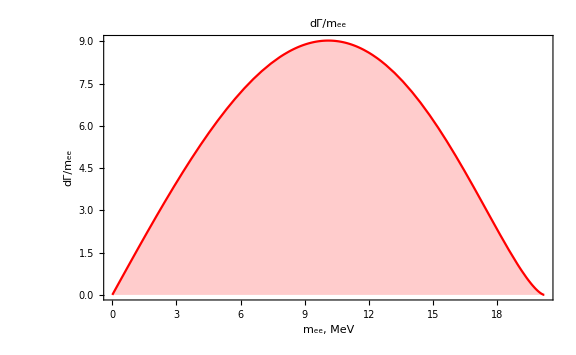

112.355

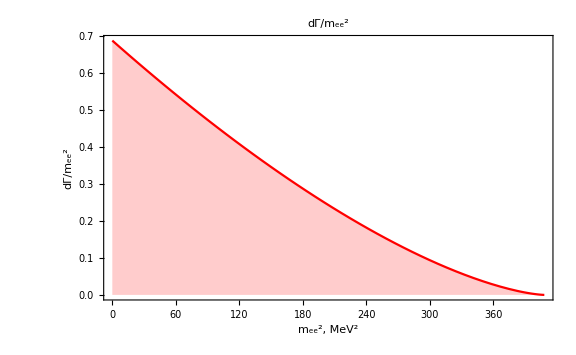

57.3399-3.75293×10^8 ⅈ

NormPHSP=3.58811×10^-11

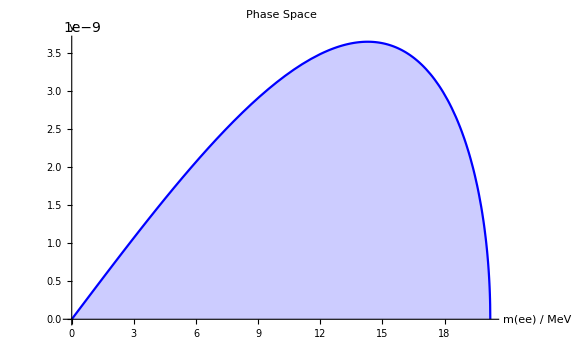

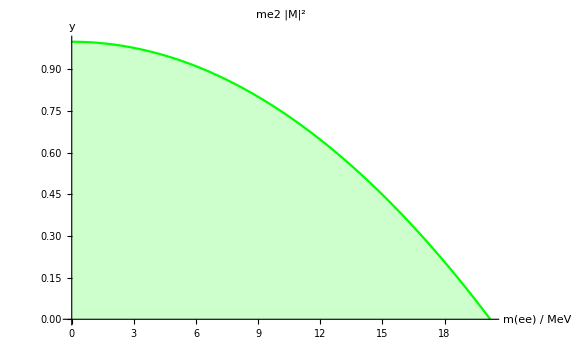

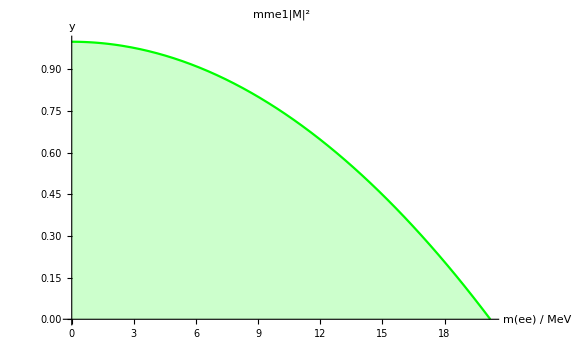

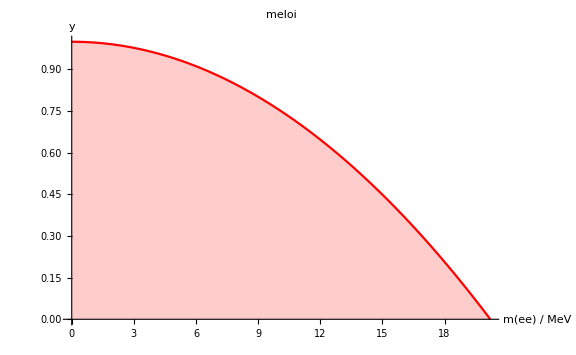

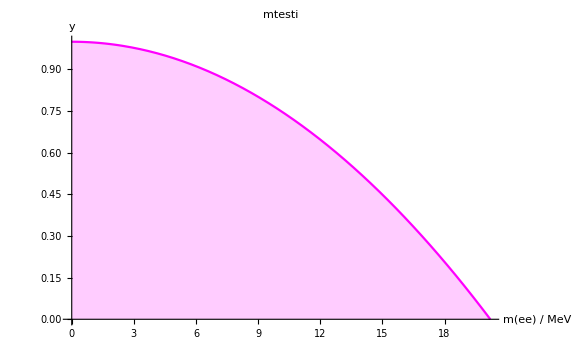

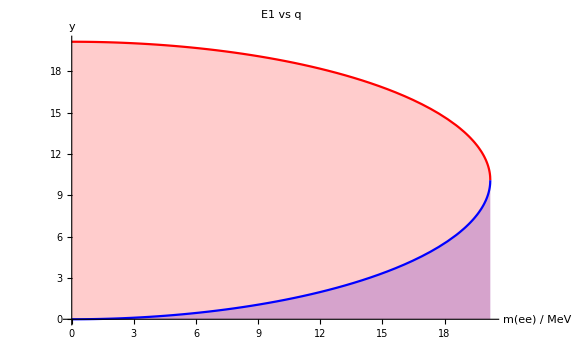

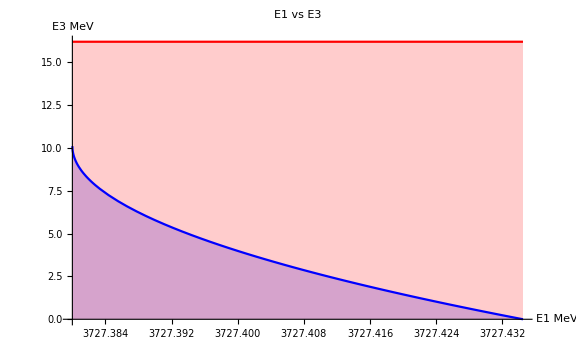

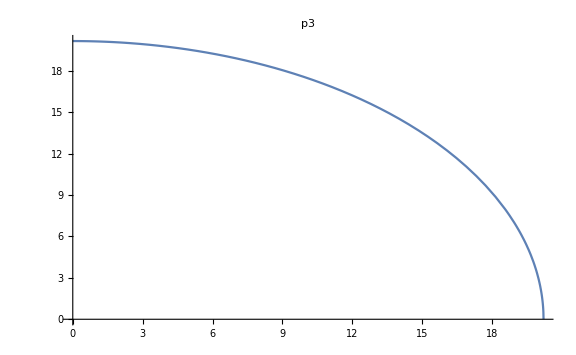

```mathematica
(* ************************************************************* *)


Plot[dgdq[q],                     {q,qmin,qmax},
PlotLabel->"dΓ/m_ee",
PlotRange->{{qmin,qmax},{0,All}},
Frame ->True, FrameLabel->{"m_ee, MeV","dΓ/m_ee"},
Filling->Axis,
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
NIntegrate[dgdq[q],{q,qmin,qmax}]

Plot[dgdq2[q2],                     {q2,q2min,q2max},
PlotLabel->"dΓ/m_ee^2",
PlotRange->{{q2min,q2max},{0,All}},
Frame ->True, FrameLabel->{"m_ee^2, MeV^2","dΓ/m_ee^2"},
Filling->Axis,
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
NIntegrate[dgdq[q2],{q2,q2min,q2max}]

Print["NormPHSP=",normphsp]
Plot[phs[q],                   {q,qmin,qmax},
PlotLabel->"Phase Space",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue}
]
Plot[me2[q]/n2,                   {q,qmin,qmax},
PlotLabel->"me2 |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Green}
]
Plot[mme1[q]/n2,                   {q,qmin,qmax},
PlotLabel->"mme1|M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Green}
]
Plot[{mel0i[q]}/n2,                   {q,qmin,qmax},
PlotLabel->"meloi",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]

Plot[mtesti[q]/n2,                   {q,qmin,qmax},
PlotLabel->"mtesti",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta}
]



Plot[{e1min[q],e1max[q]},                   {q,qmin,qmax},
PlotLabel->"E1 vs q",
FrameLabel->{"mm(ee) MeV","E1"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red}
]
Plot[{e1min[Sqrt[2m(m-x3)-(m^2-m3^2)]],e1max[Sqrt[2m(m-3727.40)-(m^2-m3^2)]]},{x3,e3min,e3max},
PlotLabel->"E1 vs E3",
FrameLabel->{"E3 MeV","E1 MeV"},
PlotRange->{{e3min,e3max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"E1 MeV","E3 MeV"},
PlotStyle->{Blue,Red}
]

Plot[p3[q],                        {q,qmin,qmax},PlotLabel->"p3"]
Plot[phs[q]*normphsp,{q,qmin,qmax},PlotLabel->"Phace Space"]
Plot[p1s[q],                      {q,qmin,qmax},PlotLabel->"P1s(q)"]

Plot[eq[q],                     {q,qmin,qmax},PlotLabel->"eq"]
Plot[pq[q],                     {q,qmin,qmax},PlotLabel->"pq"]

Plot[e3[q],                   {q,qmin,qmax},PlotLabel->"e3"]
Plot[e1min[q],             {q,qmin,qmax},PlotLabel->"e1_min"]
Plot[e1max[q],             {q,qmin,qmax},PlotLabel->"e1_max"]

Plot[gamma[q],             {q,qmin,qmax},PlotLabel->"gamma"]
Plot[vel[q],                  {q,qmin,qmax},PlotLabel->"velocity"]
Plot[p3q[q],                  {q,qmin,qmax},PlotLabel->"p3q"]
Plot[p3p1[q,1.],                {q,qmin,qmax},PlotLabel->"p3p1"]
Plot[p1q[q],                  {q,qmin,qmax},PlotLabel->"p1q"]

b=12/1000000;
min2=0;
max2=30^2;
Plot[Exp[-b*q2],                   {q2,min2,max2},
PlotLabel->"F(q2)",
FrameLabel->{"q2/GeV2","F(q2)"},
PlotRange->{{min2,max2},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q2 / GeV2",y},
PlotStyle->{Blue,Red}
]
```

```mathematica
m1
```

0.510999